## Construct and Parameterize One Enzyme Module

```mathematica
Quit[]
```

## Initializing the Notebook

```mathematica
<<Toolbox`;
<<MASSef`;

SetDirectory[NotebookDirectory[]];

removeInputFiles = True;
removeOutputFiles = True;

rxnName="PPS";
fitLabel=rxnName;
dataFileName=rxnName;

assumedUncertaintyFraction = 0.05;
(*Q10 Correction Options*)
Q10KcatCorrectionFlag = True; (*True if kcats should be corrected to physiological T*)
TPhysiological = 37; (*C*)
Q10=2.5;


(* user will need to change this path *)
(*pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef_1/";*)
pathMASSef = "/Users/guest/Desktop/internship stuff/MASSef/";
kineticDataFileName =  "kinetic_data_MASSpy.csv";

mainFolder = "fit_PPS_MASSpy_typeII";
{pathData, inputPath, outputPath}=initializeNotebook[pathMASSef, mainFolder, removeInputFiles, removeOutputFiles];
```

Molecule::shdw: Symbol Molecule appears in multiple contexts {AutomaticUnits`,System`}; definitions in context AutomaticUnits` may shadow or be shadowed by other definitions.

Working dir:/Users/guest/Desktop/internship stuff/MASSef/examples/

## Import Data

```mathematica
{rxn, mechanism, structure, nActiveSites, nAllostericSites, KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0, bufferInfo, ionCharge}= importAllData [rxnName, pathData, kineticDataFileName, assumedUncertaintyFraction, Q10KcatCorrectionFlag, TPhysiological, Q10];
```

(atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c)^PPS

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 2.20979 | 2.0993
2.32028 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.000028 | 0.0000266
0.0000294 |  | M | 7.5 | 25 |  | 
1 | pyr | 0.000083 | 0.00007885
0.00008715 |  | M | 7.5 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | pep | Null
pi | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

### Define data points priority

```mathematica
(* data point priorities should be between 0 and 1 
  if a given data point has priority 0, it will be discarded
  by default all data points priority is set to 1 *)

KeqPriorities = {1};
kmPriorities = {1,1};
s05Priorities = Null;
kcatPriorities = {1,1};
inhibitionPriorities=Null;
activationPriorities = Null;
otherParamsPriorities = Null;

{KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList}= updateDataPriorities[KeqPriorities, kmPriorities, s05Priorities, kcatPriorities, inhibitionPriorities, activationPriorities, otherParamsPriorities,
					 KeqList0,kmList0, s05List0, kcatList0, inhibitionList0, activationList0, otherParmsList0];

printEnzymeData[rxn, mechanism, structure, nActiveSites,  KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList];
```

(atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c)^PPS

;

Structure:

Active sites:

Keq Values:

Priority | Substrate | Keq_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 2.20979 | 2.0993
2.32028 | Null | Null | 7.5 | Null | Null | Null

Km Values:

Priority | Substrate | Km_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | 0.000028 | 0.0000266
0.0000294 |  | M | 7.5 | 25 |  | 
1 | pyr | 0.000083 | 0.00007885
0.00008715 |  | M | 7.5 | 25 |  |

S0.5 Values:

Priority | Substrate | S0.5_Value | Uncertainty | CoSubstrate | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

kcat Values:

Priority | Metabolite(s) | Value | Uncertainty | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations
1 | atp | Null
pyr | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  | 
1 | pep | Null
pi | Null | 30.0281 | 28.5267
31.5295 | 1/s | 7 | 37 |  |

Inhibition Values:

Priority | Parameter_Type | Inhibitor | Value | Uncertainty | Cosubstrates | Inhibition Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Activation Values:

Priority | Parameter_Type | Activator | Value | Uncertainty | Cosubstrates | Activation Type | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

Other Parameters:

Priority | Parameter_Type | Metabolite | Value | Uncertainty | Cosubstrates | Units | pH | Temperature_C | Buffer_Concentrations | Salt_Concentrations

## Define enzyme mechanism and catalytic tracks

### Define enzyme mechanism

```mathematica
Overscript[atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c, PPS]
```

(atp^c+h2o^c+pyr^c⇌amp^c+2 h^c+pep^c+pi^c)^PPS

```mathematica
catalyticBranch={"E_PPS[c] + pyr[c] <=> E_PPS[c]&pyr",
				"E_PPS[c]&pyr + atp[c] <=> E_PPS[c]&pyr&atp",

				"E_PPS[c]&pyr&atp <=> E_PPS[c]&pep&amp&pi",
				
				"E_PPS[c]&pep&amp&pi <=> E_PPS[c]&pep&amp + pi[c]",
				"E_PPS[c]&pep&amp <=> E_PPS[c]&pep + amp[c]",
				"E_PPS[c]&pep <=> E_PPS[c] + pep[c]"};


enzymeModel=constructEnzymeModule[Mechanism->catalyticBranch,Activators->{},ActivationSites->0,Inhibitors->{},InhibitionSites->0];
enzymeModel["Reactions"]
```

{((PPS^c)_^+pyr^c⇌(PPS^c&pyr^c)_^)^PPS1,((PPS^c&pep^c)_^⇌(PPS^c)_^+pep^c)^PPS2,((PPS^c&pyr^c)_^+atp^c⇌(PPS^c&pyr^c&atp^c)_^)^PPS3,((PPS^c&pep^c&amp^c)_^⇌(PPS^c&pep^c)_^+amp^c)^PPS4,((PPS^c&pyr^c&atp^c)_^⇌(PPS^c&pep^c&amp^c&pi^c)_^)^PPS5,((PPS^c&pep^c&amp^c&pi^c)_^⇌(PPS^c&pep^c&amp^c)_^+pi^c)^PPS6}

### Define all catalytic tracks

```mathematica
catalyticReactionsSet1={((PPS^c)_^+pyr^c⇌(PPS^c&pyr^c)_^)^PPS1,Overscript[(PPS^c&pep^c)_^⇌(PPS^c)_^+pep^c, PPS2],((PPS^c&pyr^c)_^+atp^c⇌(PPS^c&pyr^c&atp^c)_^)^PPS3,Overscript[(PPS^c&pep^c&amp^c)_^⇌(PPS^c&pep^c)_^+amp^c, PPS4],((PPS^c&pyr^c&atp^c)_^⇌(PPS^c&pep^c&amp^c&pi^c)_^)^PPS5,Overscript[(PPS^c&pep^c&amp^c&pi^c)_^⇌(PPS^c&pep^c&amp^c)_^+pi^c, PPS6]};
catalyticReactionsSetsList = {catalyticReactionsSet1};
```

## Set up rate equations

```mathematica
MWCFlag=False;
nActiveSites=1;
assumedSaturatingConc = 1;
simplifyFlag=True;
simplifyMaxTime=30;
otherMetsReverseZeroSub={};
otherMetsForwardZeroSub ={};

{enzymeModel, haldaneRatiosList,  metSatForSub, metSatRevSub,  finalRateConsts, metsFull, metsSub, rateConstsSub, 
			fileList, fileListSub, eqnNameList,eqnValList, eqnValListPy, 
			allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, 
			absoluteFlux, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, 
			otherAbsoluteRatesForward, otherAbsoluteRatesReverse}=

	setUpRateEquations[enzymeModel, rxn, rxnName, inputPath, inhibitionList, inhibitionList, catalyticReactionsSetsList, otherMetsReverseZeroSub,  
						 otherMetsForwardZeroSub,  MWCFlag, simplifyFlag, simplifyMaxTime, nActiveSites, assumedSaturatingConc];
```

Added inhibition reactions:

{}

Generating flux equation...

{((PPS^c&pyr^c&atp^c)_^-((PPS^c&pep^c&amp^c&pi^c)_^)/K_PPS5) Volume_c k_PPS5^⟶}

Volume_c (-(PPS^c&pep^c&amp^c&pi^c)_^ k_PPS5^⟵+(PPS^c&pyr^c&atp^c)_^ k_PPS5^⟶)

Simplifying...

Generating absolute rate forward equation...

Simplifying...

Generating absolute rate reverse equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate forward equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating relative rate reverse equation...

Simplifying...

Generating Haldane Relations...

Defining rate constant and metabolite substitutions for export...

Exporting equations...

```mathematica
flux = 0.021885655932;(*Increased Ratio by three orders of magnitude*)
FluxExpression = absoluteFlux /. {metabolite["pep", "c"] -> 0,metabolite["atp","c"]-> 0.0023217500339983896,
metabolite["pyr","c"]-> 0.000738848949329783,metabolite["amp","c"]-> 0,metabolite["pi","c"]-> 0,
     parameter["PPS_total"] -> 0.00000274626109257578, parameter["Volume", "c"] -> 1};
```

```mathematica
FluxExpression2 = parameter["v", "PPS"] /. FluxExpression;
```

## Simulate Data

```mathematica
(* format: {priority, ratio or other custom equation, value, value range (uncertainty) *)
customRatiosDataList={{5,FluxExpression2,flux,{0.9*flux,1.1*flux}}};
```

### Simulate data without uncertainty

```mathematica
{allFittingData, dataPathList, fileList, fileListSub}= simulateData[enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  
			metSatForSub, metSatRevSub,  bufferInfo, ionCharge, inputPath,  fileList, fileListSub, 
			eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
			metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating custom ratios data...

```mathematica
FilePrint@dataPathList
```

Priority	amp[c]	atp[c]	pep[c]	pi[c]	pyr[c]	param_PPS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.209787365
1	0	2.800000000000001e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.09090909090909094
1	0	4.4377009388911215e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.1368068886032101
1	0	7.033282008226834e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.20076000891310197
1	0	0.00001114700077549792	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.28474724895080133
1	0	0.000017666805645445413	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.38686317984685703
1	0	0.000028000000000000013	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.5000000000000001
1	0	0.00004437700938891122	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.6131368201531433
1	0	0.00007033282008226833	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7152527510491988
1	0	0.0001114700077549793	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7992399910868985
1	0	0.00017666805645445412	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0.00028000000000000014	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.9090909090909092
1	0	1	0	0	8.299999999999997e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.09090909090909087
1	0	1	0	0	0.000013154613497427242	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.13680688860321
1	0	1	0	0	0.000020848657381529523	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.2007600089131018
1	0	1	0	0	0.00003304289515594023	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.2847472489508011
1	0	1	0	0	0.000052369459591856	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.3868631798468568
1	0	1	0	0	0.00008299999999999997	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.4999999999999999
1	0	1	0	0	0.00013154613497427242	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.6131368201531431
1	0	1	0	0	0.00020848657381529524	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.7152527510491987
1	0	1	0	0	0.0003304289515594027	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.7992399910868982
1	0	1	0	0	0.0005236945959185599	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.86319311139679
1	0	1	0	0	0.0008299999999999997	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.9090909090909091
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932
5	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt"	0.021885655932

### Simulate data with uncertainty

```mathematica
nSamples=10;
SeedRandom[1234];
{allFittingDataList, dataPathList, fileList, fileListSub}=simulateDataWithUncertainty[nSamples,enzymeModel,dataFileName,fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, otherParmsList, rxn, metsFull,  metSatForSub, metSatRevSub, otherParmsList,  bufferInfo, ionCharge, inputPath,  fileList, 
							fileListSub, eqnNameList,eqnValList, eqnValListPy, eqnNameList, rateConstsSub, 
							metsSub, allCatalyticReactions,nonCatalyticReactions, unifiedRateConstList,  customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[1]]]
```

Priority	amp[c]	atp[c]	pep[c]	pi[c]	pyr[c]	param_PPS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	2.1536216964206223
1	0	2.576854492366368e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.09090909090909093
1	0	4.084039142914297e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.1368068886032101
1	0	6.4727658353495925e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.20076000891310192
1	0	0.000010258642508840424	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.2847472489508013
1	0	0.000016258852676153394	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.386863179846857
1	0	0.000025768544923663682	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.5000000000000001
1	0	0.000040840391429142966	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.6131368201531432
1	0	0.00006472765835349592	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7152527510491988
1	0	0.00010258642508840435	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7992399910868982
1	0	0.00016258852676153394	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0.0002576854492366368	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.9090909090909091
1	0	1	0	0	9.411378004418231e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.09090909090909083
1	0	1	0	0	0.00001491602893088072	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.13680688860320994
1	0	1	0	0	0.000023640312711105885	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.20076000891310172
1	0	1	0	0	0.00003746737068348366	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.2847472489508015
1	0	1	0	0	0.00005938178073567026	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.38686317984685664
1	0	1	0	0	0.00009411378004418232	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.4999999999999997
1	0	1	0	0	0.0001491602893088072	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.6131368201531429
1	0	1	0	0	0.00023640312711105884	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.7152527510491987
1	0	1	0	0	0.0003746737068348362	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.799239991086898
1	0	1	0	0	0.0005938178073567026	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.8631931113967898
1	0	1	0	0	0.0009411378004418232	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.909090909090909
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	28.384724987830808
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.184505592504767

### Parameter scan

```mathematica
paramScanList={{"Km",1,{0.1,1,100}},
				{"Km",2,{0.01,1,100}},
				{"Km",3,{0.01,10,100}},
				{"kcat",1,{0.01,1,100}},
				{"customRatio",1,{0.01,1,100}},
				{"Keq",1,{0.01,0.1,100}},
				{"other",1,{10^-8,10.^-6,10^-4}}};

{allFittingDataList, dataPathList, fileList, fileListSub}=simulateParameterScanData[paramScanList, enzymeModel, dataFileName, 
						  fitLabel, haldaneRatiosList, KeqList, kmList, s05List, kcatList, inhibitionList, activationList, 
						  otherParmsList, rxn, metsFull, metSatForSub, metSatRevSub,  bufferInfo, 
						  ionCharge, inputPath, fileList, fileListSub, eqnNameList, 
						  eqnValList, eqnValListPy, eqnNameList, rateConstsSub, metsSub, allCatalyticReactions,
						  nonCatalyticReactions, unifiedRateConstList, customRatiosDataList, assumedSaturatingConc];
```

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,atp,0.000028,{0.0000266,0.0000294},{},M,7.5,25,{},{}},{1,pyr,0.000083,{0.00007885,0.00008715},{},M,7.5,25,{},{}}} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,atp,0.000028,{0.0000266,0.0000294},{},M,7.5,25,{},{}},{1,pyr,0.000083,{0.00007885,0.00008715},{},M,7.5,25,{},{}}} does not exist.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Set::partw: Part 3 of {{1,atp,0.000028,{0.0000266,0.0000294},{},M,7.5,25,{},{}},{1,pyr,0.000083,{0.00007885,0.00008715},{},M,7.5,25,{},{}}} does not exist.

General::stop: Further output of Set::partw will be suppressed during this calculation.

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

Simulating Keq data...

Simulating Km data...

Simulating kcat data...

```mathematica
FilePrint[dataPathList[[18]]]
```

Priority	amp[c]	atp[c]	pep[c]	pi[c]	pyr[c]	param_PPS_total	param_pH	param_Temp	FileFlag	Target_Data
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	0	0	0	0	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt"	100.
1	0	2.800000000000001e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.09090909090909094
1	0	4.4377009388911215e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.1368068886032101
1	0	7.033282008226834e-6	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.20076000891310197
1	0	0.00001114700077549792	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.28474724895080133
1	0	0.000017666805645445413	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.38686317984685703
1	0	0.000028000000000000013	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.5000000000000001
1	0	0.00004437700938891122	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.6131368201531433
1	0	0.00007033282008226833	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7152527510491988
1	0	0.0001114700077549793	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.7992399910868985
1	0	0.00017666805645445412	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.86319311139679
1	0	0.00028000000000000014	0	0	1	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt"	0.9090909090909092
1	0	1	0	0	8.299999999999997e-6	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.09090909090909087
1	0	1	0	0	0.000013154613497427242	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.13680688860321
1	0	1	0	0	0.000020848657381529523	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.2007600089131018
1	0	1	0	0	0.00003304289515594023	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.2847472489508011
1	0	1	0	0	0.000052369459591856	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.3868631798468568
1	0	1	0	0	0.00008299999999999997	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.4999999999999999
1	0	1	0	0	0.00013154613497427242	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.6131368201531431
1	0	1	0	0	0.00020848657381529524	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.7152527510491987
1	0	1	0	0	0.0003304289515594027	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.7992399910868982
1	0	1	0	0	0.0005236945959185599	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.86319311139679
1	0	1	0	0	0.0008299999999999997	1	7.5	25	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt"	0.9090909090909091
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	0	1	0	0	1	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786
1	1	0	1	1	0	1	7	37	"/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt"	30.028110849535786

## Configure the Particle Swarm Optimization and Levenberg-Marquardt Algorithm

```mathematica
numFits=20;
lowerParamBound=-6;
upperParamBound=9;
{psoParameterPath,psoResultsFile, psoTrialSummaryFileName}  = 
definePSOparameters[inputPath, outputPath, finalRateConsts, fileList, numFits,lowerParamBound, upperParamBound, fitLabel];
{lmaParameterPath, lmaResultsFile} = defineLMAparameters[inputPath, outputPath, finalRateConsts, fileList, lowerParamBound, upperParamBound, fitLabel];
```

```mathematica
(*Print the Parameter File (Optional) *)
FilePrint[psoParameterPath]
```

num_Cpus	1
temperature_correction	False
num_trial	20
num_generations	2000
val_pop_size	20
bestFitnessCutoff	1.1
val_neigh_size	3
val_inertia	1
val_cogn_rate	2.1
val_soc_rate	2.1
use_Keep_Best	True
use_Random_Replace	True
percent_Rand	0.05
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_amp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_pi.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

```mathematica
(*Optional*)
FilePrint[lmaParameterPath]
```

num_Cpus	1
temperature_correction	False
xtol_value	1.e-15
ftol_value	1.e-7
gtol_value	1.e-7
epsfcn_min_value	7
maxfev_value	1000
lower_bound	-6
upper_bound	9
num_func_var	12
filesWithFunctions	[/Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateFor.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/absRateRev.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_atp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateFor_pyr.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_amp.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_pep.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/relRateRev_pi.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/haldaneRatio_1.txt, /Users/guest/Desktop/internship stuff/MASSef/examples/fit_PPS_MASSpy_typeII/input/customRatio_1.txt]
value_row	-1
function_row	-2
data_row_high	-2

## Fit the model

```mathematica
runFit[inputPath, pathMASSef, psoParameterPath ,lmaParameterPath,psoTrialSummaryFileName, 
		psoResultsFile, lmaResultsFile, numFits, dataPathList]
```

best_fit: 63.8006162603
best_fit: 63.8009400336
best_fit: 64.5529485723
best_fit: 63.8007720169
best_fit: 63.8781706645
best_fit: 63.807751784
best_fit: 63.8020900362
best_fit: 64.4980738776
best_fit: 63.8029883308
best_fit: 63.8035805896
best_fit: 64.4998459585
best_fit: 63.8704461468
best_fit: 64.9521702667
best_fit: 63.8007026292
best_fit: 63.8337034628
best_fit: 63.8080454786
best_fit: 64.498053545
best_fit: 63.8005892105
best_fit: 64.4999863178
best_fit: 63.8145633608

## Evaluate fit results

```mathematica
(* run for simple simulated data, no uncertainty or parameter scan*)
lmaResultsFileNew=lmaResultsFile;
dataFilePath = dataPathList;
```

```mathematica
(* run only for data simulated with uncertainty or parameter scan *)
datasetI=2;
lmaResultsFileNew=StringTake[lmaResultsFile,;;-5]<>"_"<>ToString[datasetI] <>".txt";
dataFilePath = dataPathList[[datasetI]];
```

```mathematica
flagFitType = "log_ssd";
{flagFitLocal, msgLocal, fittingData, filteredDataList, bestFitDetails}=getRatesWithSSD[rxnName, lmaResultsFileNew, dataFilePath, inputPath, outputPath,  fileListSub, 
				rateConstsSub, metsSub, flagFitType, Null, True, ""];
```

```mathematica
bestFitDetails//TableForm
```

Priority | Fitting Equation | Log10 residual | Log10 residual^2 | Euclidean residual | Relative error | True value | Predicted Value
 |  |  |  |  |  |  | 
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | haldaneRatio_1 | 0.000560835 | 3.14535×10^-7 | 0.0028555 | 0.12922 | 2.20979 | 2.21264
1 | relRateFor_atp | 0.0643032 | 0.0041349 | 0.0145079 | 15.9587 | 0.0909091 | 0.105417
1 | relRateFor_atp | 0.0608186 | 0.0036989 | 0.0205648 | 15.032 | 0.136807 | 0.157372
1 | relRateFor_atp | 0.0560094 | 0.00313706 | 0.027635 | 13.7652 | 0.20076 | 0.228395
1 | relRateFor_atp | 0.0497736 | 0.00247741 | 0.0345779 | 12.1434 | 0.284747 | 0.319325
1 | relRateFor_atp | 0.0423104 | 0.00179017 | 0.0395865 | 10.2327 | 0.386863 | 0.42645
1 | relRateFor_atp | 0.0341888 | 0.00116887 | 0.0409521 | 8.19041 | 0.5 | 0.540952
1 | relRateFor_atp | 0.0262163 | 0.000687292 | 0.0381521 | 6.22244 | 0.613137 | 0.651289
1 | relRateFor_atp | 0.0191439 | 0.000366489 | 0.0322339 | 4.50665 | 0.715253 | 0.747487
1 | relRateFor_atp | 0.0134122 | 0.000179888 | 0.0250678 | 3.13646 | 0.79924 | 0.824308
1 | relRateFor_atp | 0.00909792 | 0.0000827721 | 0.0182735 | 2.11697 | 0.863193 | 0.881467
1 | relRateFor_atp | 0.00602784 | 0.0000363349 | 0.0127058 | 1.39764 | 0.909091 | 0.921797
1 | relRateFor_pyr | 0.370673 | 0.137398 | 0.122533 | 134.786 | 0.0909091 | 0.213442
1 | relRateFor_pyr | 0.342083 | 0.11702 | 0.163933 | 119.828 | 0.136807 | 0.30074
1 | relRateFor_pyr | 0.305145 | 0.0931133 | 0.204582 | 101.904 | 0.20076 | 0.405342
1 | relRateFor_pyr | 0.260966 | 0.0681035 | 0.234562 | 82.3755 | 0.284747 | 0.519309
1 | relRateFor_pyr | 0.212681 | 0.045233 | 0.24444 | 63.1851 | 0.386863 | 0.631303
1 | relRateFor_pyr | 0.16479 | 0.0271559 | 0.230736 | 46.1472 | 0.5 | 0.730736
1 | relRateFor_pyr | 0.121661 | 0.0148013 | 0.198231 | 32.3307 | 0.613137 | 0.811368
1 | relRateFor_pyr | 0.0860992 | 0.00741306 | 0.156832 | 21.9268 | 0.715253 | 0.872085
1 | relRateFor_pyr | 0.058887 | 0.00346768 | 0.116062 | 14.5215 | 0.79924 | 0.915302
1 | relRateFor_pyr | 0.0392525 | 0.00154076 | 0.0816516 | 9.45925 | 0.863193 | 0.944845
1 | relRateFor_pyr | 0.025689 | 0.000659923 | 0.0553959 | 6.09355 | 0.909091 | 0.964487
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateFor | 2.35151 | 5.52958 | 6715.77 | 22365. | 30.0281 | 6745.8
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
1 | absRateRev | 0.00100804 | 1.01615×10^-6 | 0.0697793 | 0.23238 | 30.0281 | 30.0979
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617
5 | customRatio_1 | 0.0942284 | 0.008879 | 0.00426869 | 19.5045 | 0.0218857 | 0.017617

### Simulated Data and Best Fit Data Plot

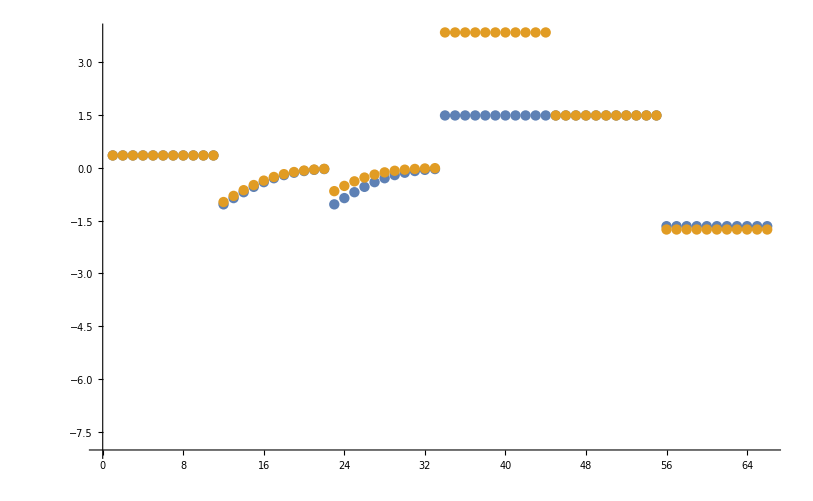

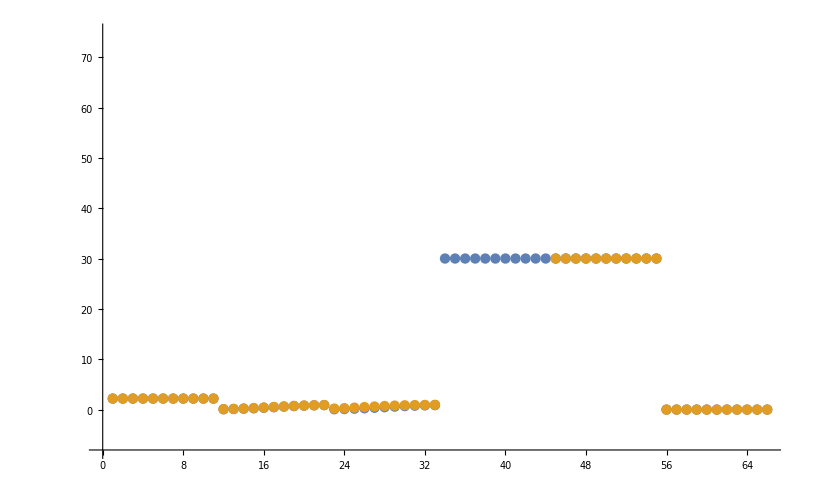

```mathematica
dataSetI=6;
ListPlot[Log10[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}], AxesOrigin->{0,-8}]
ListPlot[{fittingData[[All,-1]],filteredDataList[[dataSetI,3]]}, AxesOrigin->{0,-8}]
```

### Parameter Distribution

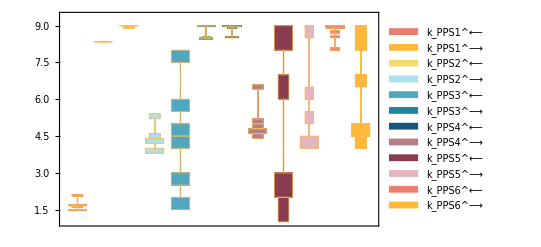

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[1;;6,2]]]],ChartElementFunction->"HistogramDensity","PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24]
```

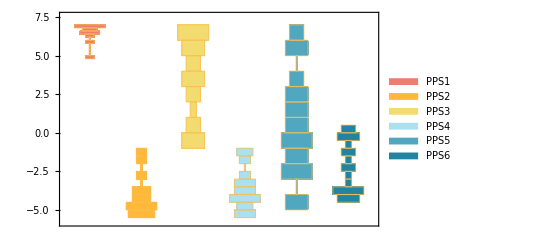

```mathematica
{ratios, plotLegend} = getElementaryKeqs[filteredDataList, rateConstsSub];
DistributionChart[Log10[Transpose@ratios],ChartElementFunction->"HistogramDensity",ChartLegends-> plotLegend,ChartStyle-> 24](*Histogram*)
```

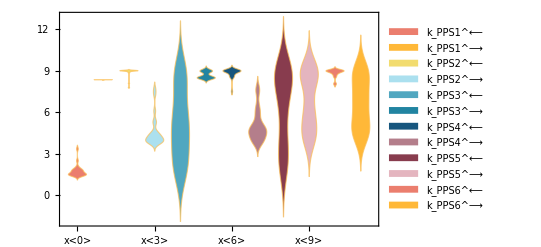

```mathematica
DistributionChart[Transpose[Log10[filteredDataList[[All,2]]]],ChartLabels-> rateConstsSub[[All,2]],"PlotRange"->{-7,10},ChartLegends-> rateConstsSub[[All,2]]/.Reverse/@rateConstsSub,ChartStyle-> 24](*Smooth*)(*If the distribution is narrow, the smooth Kernel outputs an error*)
```

### Data Error Distribution

```mathematica
errors=
Table[
	fittingData[[i,-1]]-filteredDataList[[j,3,i]],
 {j,1,Length@filteredDataList},{i,1,Length@filteredDataList[[1,3]]}];
```

```mathematica
funcNames=
Table[
	StringCases[func,RegularExpression[FileNameJoin[{inputPath , "(.*)\\.txt"}, OperatingSystem->$OperatingSystem]]->"$1"][[1]],{func,fittingData[[All,-2]]}]; (* fix later*);
```

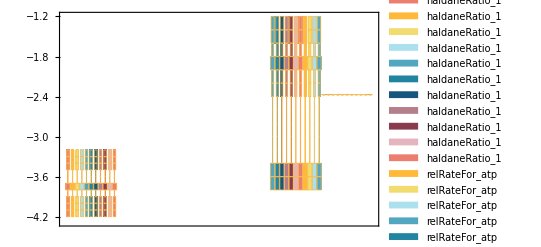

```mathematica
DistributionChart[Transpose[Log10[errors]],ChartElementFunction->"HistogramDensity",ChartLegends-> funcNames,ChartStyle-> 24](*Histogram*)
```

#### Cluster Parameters

```mathematica
(*clusters=FindClusters[Log10[filteredDataListRed[[All,2]]],Method->{"Agglomerate","Linkage"->"Complete","SignificanceTest"->{"Gap","Tolerance"->0.0001}}];(**)*)
clusters=FindClusters[Log10[filteredDataList[[1;;6,2]]],Method->{"Optimize","Iterations"->2}];
medianParamCluster=Table[Median[clusters[[cluster,All,param]]],{cluster,Length[clusters]},{param,Length[clusters[[1,1]]]}](*Switch to log space and use mean?*);
clusterSqdRes=Table[(clusters[[cluster,paramSet,param]]-medianParamCluster[[cluster,param]])^2,{cluster,Length[clusters]},{paramSet,Length[clusters[[cluster]]]},{param,Length[clusters[[1,1]]]}];
clusterSSE=Table[Total[clusterSqdRes[[cluster,paramSet]]],{cluster,Length[clusterSqdRes]},{paramSet,Length[clusterSqdRes[[cluster]]]}];
bestClusterSSE=Table[SortBy[clusterSSE[[cluster]],Less],{cluster,Length[clusterSSE]}][[All,1]];
finalClusterParams={};
Table[If[clusterSSE[[cluster,paramSet]]==bestClusterSSE[[cluster]],finalClusterParams=Append[finalClusterParams,clusters[[cluster,paramSet]]]],{cluster,Length[clusterSSE]},{paramSet,Length[clusterSSE[[cluster]]]}];
```

#### Print Representative Parameter Sets for Each Cluster (Optional)

```mathematica
TableForm[finalClusterParams]
```

2.0647 | 8.3435 | 8.92297 | 4.25533 | 5.57733 | 8.97432 | 8.99998 | 4.74547 | 1.76518 | 5.21355 | 8.02095 | 4.16384
1.49434 | 8.34818 | 8.90825 | 5.24011 | 2.89795 | 8.49354 | 8.51834 | 4.59581 | 8.5967 | 4.07595 | 8.9936 | 8.99983

#### Parameter Cluster Plots (Optional)

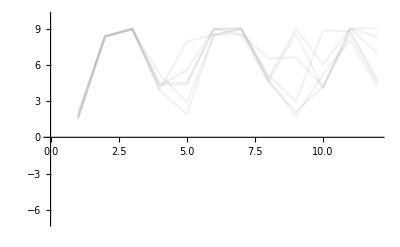

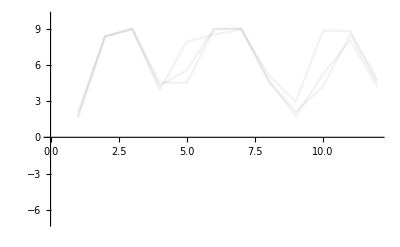
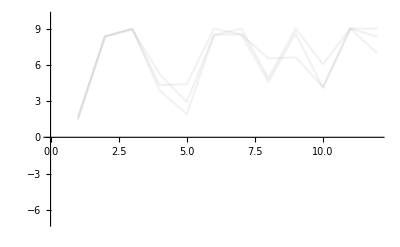

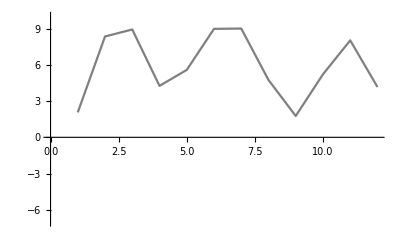
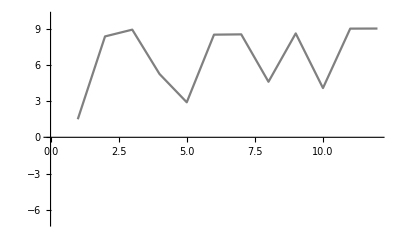

```mathematica
ListPlot[Log10[filteredDataList[[1;;6,2]]],"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]](*All parameter sets*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[.1,Gray]]&/@clusters
(*All parameter set clusters*)
ListPlot[#,"Joined"-> True,"PlotRange"->{-7,10},PlotStyle->Opacity[1,Gray]]&/@finalClusterParams(*Representative parameter sets*)
```

### Recalculate Enzyme Parameters for all Candidate Rate Constant Sets

```mathematica
enzymeSub= parameter[rxnName<>"_total"]-> 1;
assumedSaturatingConc=1;
paramSet = 1;
dataHeader = Import[dataFilePath][[1]];
paramFitSub=Thread[rateConstsSub[[All,1]]->filteredDataList[[paramSet,2]]];
```

```mathematica
backCalculateKms[rxn, kmList, relativeRateForward, relativeRateReverse,metSatForSub, metSatRevSub, paramFitSub, assumedSaturatingConc, rxnName]//TableForm
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

data value | predicted value | error in %
0.000028 | 0.0000237607 | 15.1404
0.000083 | 0.0000305857 | 63.1497

```mathematica
backCalculateKcats[rxn, kcatList, absoluteRateForward, absoluteRateReverse, paramFitSub, enzymeSub, assumedSaturatingConc]//TableForm
```

data value | predicted value | error in %
30.0281 | 6745.8 | 22365.
30.0281 | 0. | 100.

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1,3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.20979 | 2.21264 | 0.12922

```mathematica
backCalculateRatios[haldaneRatiosList[[1]], KeqList[[1]][[3]], paramFitSub]//TableForm
```

data value | predicted value | error in %
2.20979 | 2.21264 | 0.12922

```mathematica
backCalculateKic[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

```mathematica
backCalculateKiu[fittingData, filteredDataList[[1]], dataHeader, inhibitionList]//TableForm
```

data value | predicted value | error in %

#### Export rate back calculated parameter error distribution

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

General::stop: Further output of Solve::ratnz will be suppressed during this calculation.

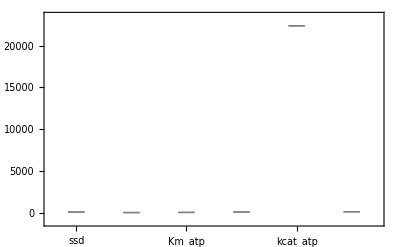

```mathematica
dataHeader = Import[dataFilePath][[1]];

{predictedParameters, predictedParameterErrors} = exportPredictedParametersAndErrors[rxn, rxnName, fitLabel, flagFitType, numFits,KeqList, kmList,s05List, kcatList, inhibitionList, otherParmsList, absoluteRateForward, absoluteRateReverse, relativeRateForward, relativeRateReverse, haldaneRatiosList,  metSatForSub, metSatRevSub, rateConstsSub, assumedSaturatingConc, fittingData, filteredDataList, dataHeader];

BoxWhiskerChart[Transpose@predictedParameterErrors[[3;;]], ChartLabels->{predictedParameterErrors[[1]]}]
```

## Export data

```mathematica
directoryExport = "/Users/guest/Desktop/internship stuff/MASSef/examples/"
CreateDirectory[directoryExport<>ToLowerCase[rxnName]]
indexLastGoodFit = 7;
```

/Users/guest/Desktop/internship stuff/MASSef/examples/

CreateDirectory::filex: /Users/guest/Desktop/internship stuff/MASSef/examples/pps already exists.

$Failed

```mathematica
rateConstsString = ToString/@rateConstsSub[[All,1]];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_labels_"<>ToLowerCase[rxnName]<>".txt",rateConstsString]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\rateconst_labels_pps.txt

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\S_"<>ToLowerCase[rxnName]<>".txt",S[enzymeModel]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\S_pps.txt

```mathematica
ToString/@getSpecies[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\species_"<>ToLowerCase[rxnName]<>".txt",ToString/@getSpecies[enzymeModel]]
```

{E_PPS[c],E_PPS[c]&pep,E_PPS[c]&pyr,E_PPS[c]&pep&amp,E_PPS[c]&pyr&atp,amp[c],atp[c],pep[c],pi[c],pyr[c],E_PPS[c]&pep&amp&pi}

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\species_pps.txt

```mathematica
ToString/@getReactions[enzymeModel]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\reactions_"<>ToLowerCase[rxnName]<>".txt",ToString/@getReactions[enzymeModel]]
```

{PPS1: E_PPS[c] + pyr[c] <=> E_PPS[c]&pyr,PPS2: E_PPS[c]&pep <=> E_PPS[c] + pep[c],PPS3: atp[c] + E_PPS[c]&pyr <=> E_PPS[c]&pyr&atp,PPS4: E_PPS[c]&pep&amp <=> amp[c] + E_PPS[c]&pep,PPS5: E_PPS[c]&pyr&atp <=> E_PPS[c]&pep&amp&pi,PPS6: E_PPS[c]&pep&amp&pi <=> E_PPS[c]&pep&amp + pi[c]}

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\reactions_pps.txt

```mathematica
solEnz = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/enzSol_"<>rxnName<>"_.m"];
```

```mathematica
speciesStrings = ToString/@solEnz[[All,1]]
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_labels_"<>ToLowerCase[rxnName]<>".txt",ToString/@solEnz[[All,1]]];
```

{E_PPS[c],E_PPS[c]&pep,E_PPS[c]&pyr,E_PPS[c]&pep&amp,E_PPS[c]&pyr&atp,E_PPS[c]&pep&amp&pi}

```mathematica
pythonSubList = Thread[Variables[solEnz[[1,2]]]->(ToString/@Variables[solEnz[[1,2]]])];
ToPython[solEnz[[1,2]]/.pythonSubList]
Do[
Export[directoryExport <>ToLowerCase[rxnName]<>"\\equation_"<>speciesStrings[[i]]<>"_"<>ToLowerCase[rxnName]<>".txt",ToPython[solEnz[[i,2]]/.pythonSubList]];,{i,1,Length[solEnz]}]
```

-((-(k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*param_PPS_total) - k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*param_PPS_total - k_PPS1_rev*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*param_PPS_total - atp(c)*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*param_PPS_total - k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*param_PPS_total*pi(c) - amp(c)*k_PPS1_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*param_PPS_total*pi(c))/(k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev + k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd + k_PPS1_rev*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd + atp(c)*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*pep(c) + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS6_fwd*pep(c) + k_PPS1_rev*k_PPS2_rev*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pep(c) + atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pep(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pep(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pep(c) + k_PPS1_rev*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pi(c) + amp(c)*k_PPS1_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pep(c)*pi(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pep(c)*pi(c) + k_PPS1_rev*k_PPS2_rev*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS1_rev*k_PPS2_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*atp(c)*k_PPS2_rev*k_PPS3_fwd*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + amp(c)*k_PPS2_rev*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pep(c)*pi(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_rev*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS5_rev*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS6_fwd*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS4_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_fwd*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_fwd*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_fwd*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_fwd*k_PPS6_rev*pi(c)*pyr(c) + atp(c)*k_PPS1_fwd*k_PPS2_fwd*k_PPS3_fwd*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + k_PPS1_fwd*k_PPS2_fwd*k_PPS3_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*atp(c)*k_PPS1_fwd*k_PPS3_fwd*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c) + amp(c)*k_PPS1_fwd*k_PPS3_rev*k_PPS4_rev*k_PPS5_rev*k_PPS6_rev*pi(c)*pyr(c)))

```mathematica
(*NEED TO GRAB THE RATE CONST DATA FROM CLUSTERS*)
```

```mathematica
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateconst_clusters_"<>ToLowerCase[rxnName]<>".txt",filteredDataList[[1;;indexLastGoodFit,2]]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\rateconst_clusters_pps.txt

```mathematica
solRateEq = Import["/Users/guest/Desktop/internship stuff/MASSef/examples/"<>mainFolder <>"/input/absoluteFlux_"<>rxnName<>"_.m"];
pythonSubList = Thread[Variables[solRateEq[[2]]]->(ToString/@Variables[solRateEq[[2]]])];
Export[directoryExport <>ToLowerCase[rxnName]<>"\\rateLaw_"<>ToLowerCase[rxnName]<>".txt",ToPython[solRateEq[[2]]/.pythonSubList]]
```

/Users/guest/Desktop/internship stuff/MASSef/examples/pps\rateLaw_pps.txt